# Träger für Märklin Glaskasen

## Radstand Glaskasten

```mathematica
h0=Round[1435/16.5]
```

87

```mathematica
tol=Quantity[0.1,"Millimeters"]
```

0.1 mm

#### Achsabstand

```mathematica
Quantity[3200,"Millimeters"]/87.
```

36.7816 mm

```mathematica
l=Round[UnitConvert[Quantity[1.45,"Inches"],"Millimeters"],tol]
```

36.8 mm

#### Spurkranzabstand

```mathematica
s=Round[UnitConvert[Quantity[0.63,"Inches"],"Millimeters"],tol]
```

16. mm

#### Innenseite Spurkränze

```mathematica
sInnen=Round[UnitConvert[Quantity[0.55,"Inches"],"Millimeters"],tol]
```

14. mm

#### Außenseite Spurkränze

```mathematica
sAussen=Round[UnitConvert[Quantity[0.64,"Inches"],"Millimeters"],tol]
```

16.3 mm

#### Raddurchmesser außen

```mathematica
dAussen=Round[UnitConvert[Quantity[0.43,"Inches"],"Millimeters"],tol]
```

10.9 mm

#### Spurkranzdurchmesser

```mathematica
dSpurkranz=Round[UnitConvert[Quantity[0.55,"Inches"],"Millimeters"],tol]
```

14. mm

#### Mitte Spurkranzöffnung

```mathematica
sMitte=(sInnen+sAussen)/2
```

15.15 mm

#### Breite Spurkranzöffnung

```mathematica
b=sAussen-sInnen
```

2.3 mm

#### Länge Spurkranzöffnung

```mathematica
c=Round[2 √((dSpurkranz/2)^2-(dAussen/2)^2),tol]
```

8.8 mm

#### Länge Schleifer

```mathematica
lSchleifer=Quantity[68,"Millimeters"]
```

68 mm

#### Breite Schleifer

```mathematica
wSchleifer=Quantity[7,"Millimeters"]
```

7 mm

## Halterung

```mathematica
points={{-l,-sMitte},{-l,sMitte},{l,sMitte},{l,-sMitte}}/2
```

{{-18.4 mm,-7.575 mm},{-18.4 mm,7.575 mm},{18.4 mm,7.575 mm},{18.4 mm,-7.575 mm}}

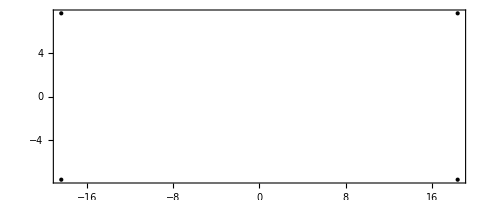

```mathematica
Show[Graphics[Point[points/Quantity["Millimeters"]]],Frame->True]
```

#### Spurkranzöffnung

```mathematica
oeffnung={{-c,-b},{-c,b},{c,b},{c,-b}}/2
```

{{-4.4 mm,-1.15 mm},{-4.4 mm,1.15 mm},{4.4 mm,1.15 mm},{4.4 mm,-1.15 mm}}

```mathematica
schleifer=1/2.{{-lSchleifer,-wSchleifer},{-lSchleifer,wSchleifer},{lSchleifer,wSchleifer},{lSchleifer,-wSchleifer}}
```

{{-34. mm,-3.5 mm},{-34. mm,3.5 mm},{34. mm,3.5 mm},{34. mm,-3.5 mm}}

```mathematica
Oeffnungen=Append[Function[point,(point+#)/Quantity["Millimeters"]&/@oeffnung]/@points,schleifer/Quantity["Millimeters"]]
```

{{{-22.8,-8.725},{-22.8,-6.425},{-14.,-6.425},{-14.,-8.725}},{{-22.8,6.425},{-22.8,8.725},{-14.,8.725},{-14.,6.425}},{{14.,6.425},{14.,8.725},{22.8,8.725},{22.8,6.425}},{{14.,-8.725},{14.,-6.425},{22.8,-6.425},{22.8,-8.725}},{{-34.,-3.5},{-34.,3.5},{34.,3.5},{34.,-3.5}}}

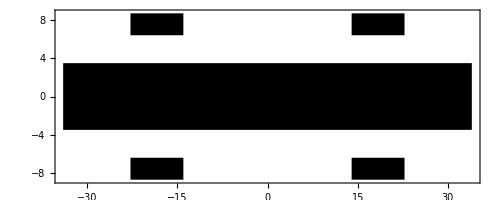

```mathematica
Graphics[Polygon[##]&/@Oeffnungen,Frame->True]
```

```mathematica
Export["oeffnungen.csv",Oeffnungen,"CSV"]
```

oeffnungen.csv

```mathematica
Directory[]
```

/home/cmaier/scad/Maerklin/mechanical